# The Structure of Tensor-Valued Functions on Tensors

## Abstract

technical tools: Given an explicit isotypic decomposition of an SO(3)-representation X, we construct an explicit isotypic decomposition of the symmetric power S^D(X).

## Notation

G:=SO(3)

𝔖^d:= the symmetric group on d symbols

Λ:=ℕ_0, λ,μ,ν∈Λ

H_λ:={A∈𝒮^λ(ℂ^3)|tr A=0} the irreducible representation of G of dimension 2λ+1

X,Y:= finite dimensional G-representations

Hom^G(X,Y):= the set of G-equivariant linear maps from X to Y

X^G:= the set of points in X fixed by all of G

## Problem Statement

Definition: Let

R:=(𝒮(X^*))^G≅Hom^G(𝒮(X),ℝ)

be the set of invariant polynomial functions from X to ℝ, and let

M:=(𝒮(X^*)⊗Y)^G≅Hom^G(𝒮(X),Y)

be the set of equivariant polynomial functions from X to Y.

Problem 1: Find minimal generating sets for R as an ℝ-algebra and M as an R-module.

## Nakayama’s Lemma

Lemma (Nakayama’s Lemma): Let M=⊕_(D∈ℕ_0)M^D be a finitely generated graded module over a graded ring R=⊕_(D∈ℕ_0)R^D, where R_0=ℝ. Let I:=⊕_(D∈ℕ)R^D be the ideal generated by the positively graded elements of R. Let L⊆M. Then L/I M generates M/I M as an ℝ-module iff L generates M as an R-module.

Algorithm (Reduction from Problem 1 to Problem 2): Suppose that we are given bases ℛ_D,ℳ_D for R^D,M^D as ℝ-modules. Note that

(I M)^D:=I M∩M^D=∑_(1<=D'<=D) R_D' M_(D-D'),
I M=⊕_(D∈ℕ)(I M)^D,
M/I M≅⊕_(D∈ℕ)M^D/(I M)^D.

Moreover,

(I M)^D=Span{r_D' m_(D-D')|1<=D'<=D,r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D')}.

Now, define

D_max:=max{D∈ℕ|M^D/(I M)^D!=0},

We have a Hilbert series for M_D, we need one for (I M)_D to get these degrees.

which may be difficult to determine in practice. For each 1<=D<=D_max, compute a basis for (I M)_D and extend it to a basis for M^D by adjoining the basis vectors in the set L_D⊆M^D. Write L:=∪_(D∈ℕ)L_D. Since L_D/(I M)_D is a basis for M^D/(I M)_D, L/I M is a basis for M/I M, so by Nakayama’s Lemma, L is a minimal generating set for M as an R-module.

Next, apply the above algorithm with M=I. Let ℝ[L] be the ℝ-algebra generated by L. Clearly, ℝ⊆ℝ[L]. Now, write R_(<=D):=R_0⊕…⊕R^D, and suppose that R_(<=D)⊆ℝ[L]. Then

R_(D+1)=I_(D+1)⊆Span_ℝ(L_(D+1))+(I^2)_(D+1)=Span_ℝ(L_(D+1))+∑_(1<=D'<=D) I_D' I_(D+1-D').

Clearly, Span_ℝ(L_(D+1))⊆ℝ[L], and by the inductive hypothesis, I_1,...,I_D⊆R_(<=D)⊆ℝ[L]. Thus, R=ℝ[L]. To see that L is minimal, note that if any L⊆I generates R as an ℝ-algebra, then L generates I as an R-module, so L/I^2 generates I/I^2 as an ℝ-module. Thus, since our given L makes L/I^2 a basis for I/I^2, our given L is a minimal generating set for R as an ℝ-algebra.

Problem 2: Find bases for R^D,M^D as ℝ-modules.

## Isotypic Decomposition

Algorithm (Reduction from Problem 2 to Problem 3): Let

X=⊕_λ H_λ⊗M_λ.

Then 𝒮^D(X^*) has some isotypic decomposition

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗N_ν^D.

Suppose that we are given bases for the multiplicity spaces N_ν^D as well as the explicit isomorphism embedding each isotypic component H_ν⊗N_ν^D into 𝒮^D(X^*). Let Y=H_ρ. Then

R^D≅H_0⊗N_0^D,
M^D≅(H_ρ⊗H_ρ)^G⊗N_ρ^D.

Thus, a basis for R^D is given by the isotypic basis vectors in 𝒮^D(X^*) corresponding to the 0-isotypic component H_0⊗N_0^D. Moreover, a basis for M^D is given as follows. First, apply the Clebsch-Gordan isomorphism H_0->(H_ρ⊗H_ρ)^G to obtain the unique G-invariant vector v in H_ρ⊗H_ρ. For each basis vector m in N_ρ^D, send v⊗m through the isomorphism above to obtain basis vectors in 𝒮^D(X^*) corresponding to M^D.

Problem 3: Find bases for N_0^D,N_ρ^D.

## Explicit Isotypic Decomposition of the Symmetric Power 𝒮^D(X)

### General Idea

We will incrementally split off multiplicity spaces. All isomorphisms below should be isomorphisms of G-modules.

### Symmetric Power to Young Symmetrizer

#### Lemma

Let D∈ℕ_0, and let X=⊕_λ H_λ⊗M_λ be finite dimensional, so λ ranges over some finite set. Then

𝒮^D(X)≅⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the outer sum is over all sequences (d_λ)_λ of nonnegative integers such that ∑_λ d_λ=D, the inner sum is over all sequences (π_λ)_λ of integer partitions of d_λ with at most min(dim H_λ,dim M_λ) parts, and e_π_λ∈ℝ[𝔖^d_λ] is any Young symmetrizer associated with π_λ. Moreover, the isomorphism is given by rearranging the tensor product and symmetrizing.

#### Proof

We have

𝒮^D(X)≅𝒮^D(⊕_λ H_λ⊗M_λ)
≅^Sym⊕_((d_λ)_λ)⊗_λ 𝒮^d_λ(H_λ⊗M_λ)
≅^(Rearrange ⊗, Sym)⊕_((d_λ)_λ)⊗_λ⊕_π_λ e_π_λ(H_λ^(⊗d_λ))⊗e_π_λ(M_λ^(⊗d_λ))
≅^(Rearrange ⊗)⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the third line is due to the Cauchy decomposition, which follows from Schur-Weyl duality.

### Young Symmetrizer to Tensor Product

#### Lemma

Let λ,d∈ℕ_0, and let π be a partition of d. Let e_π be the Young symmetrizer associated with the standard tableau T_π of shape π filled “top-down, left-right” with the values 1,...,d. Let π_p denote the number of boxes in the p^th column of T_π, i.e., the p^th part of the conjugate partition of π. Then

e_π(H_λ^(⊗d))≅⊕_((μ_p)_p)(⊗_p H_μ_p)⊗r_π(⊗_p Hom_G(H_μ_p,Λ^π_p(H_λ))),

where the sum is over all sequences (μ_p)_p of labels μ_p such that H_μ_p appears in Λ^π_p(H_λ).

#### Proof

We have

e_π(H_λ^(⊗d))=r_π(c_π(H_λ^(⊗d)))
≅r_π(⊗_p Λ^π_p(H_λ))
≅r_π(⊗_p⊕_μ_p H_μ_p⊗Hom_G(H_μ_p,Λ^π_p(H_λ)))
≅r_π(⊕_((μ_p)_p)(⊗_p H_μ_p)⊗(⊗_p Hom_G(H_μ_p,Λ^π_p(H_λ))))
≅⊕_((μ_p)_p)(⊗_p H_μ_p)⊗r_π(⊗_p Hom_G(H_μ_p,Λ^π_p(H_λ))).

#### Corollary

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅⊕_((μ_(λ,p))_(λ,p))(⊗_λ⊗_p H_(μ_(λ,p)))⊗(⊗_λ r_π_λ(⊗_p Hom_G(H_(μ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

### Tensor Product to Isotypic Component

#### Lemma

Fix any collection (μ_(λ,p))_(λ,p). Then

⊗_λ⊗_p H_(μ_(λ,p))≅⊕_ν H_ν⊗Hom_G(H_ν,⊗_λ⊗_p H_(μ_(λ,p))).

### Symmetric Power to Isotypic Component

#### Corollary

We have

𝒮^D(X)≅⊕_ν⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_(λ,p))_(λ,p))H_ν⊗Hom_G(H_ν,⊗_λ⊗_p H_(μ_(λ,p)))⊗(⊗_λ r_π_λ(⊗_p Hom_G(H_(μ_(λ,p)),Λ^(π_(λ,p))(H_λ))))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the sum over (μ_(λ,p))_(λ,p) is restricted such that H_ν appears in ⊗_λ⊗_p H_(μ_(λ,p)) and every H_(μ_(λ,p)) appears in Λ^(π_(λ,p))(H_λ)

## Algorithm: Basis for an Isotypic Component of the Symmetric Power 𝒮^D(X)

Given D∈ℕ_0 and ν∈ℕ_0,

place D at the root of a tree;

for each leaf, and for each possible (d_λ)_λ at that leaf, spawn a new leaf containing (d_λ)_λ;

for each leaf, and for each possible (π_λ)_λ at that leaf, spawn a new leaf containing (π_λ)_λ;

for each leaf, and for each possible (μ_(λ,p))_(λ,p) at that leaf, spawn a new leaf containing (μ_(λ,p))_(λ,p);

prune all leaves such that ν does not belong in (μ_(λ,p))_(λ,p)

#### Optimizations

For Hom_G(H_ν,⊗_λ⊗_p H_(μ_(λ,p))) that are absolutely necessary to compute, compute via tensor train, memoize Clebsch Gordan tensors
For Hom_G(H_(μ_(λ,p)),Λ^(π_(λ,p))(H_λ)), use antisymmetrized components

## Code

#### Helper Functions

```mathematica
ClearAll[AncestralNestTree,SchurS,validPaths,containsIsotypicComponentQ,hλdλ,tensorMultiply,changeBasis]
SetAttributes[{Λ,ℐ},Listable];
```

```mathematica
AncestralNestTree=ResourceFunction["AncestralNestTree"];
SchurS=ResourceFunction["SchurS"];
```

```mathematica
Λ[λ_Integer?NonNegative,dλ_Integer?NonNegative]:=If[dλ==1,{λ},Range[0,λ dλ],changeBasis]
ℐ[a_,b_Integer?NonNegative]:=Range[Abs[a-b],a+b]
```

```mathematica
(*Eventually try to generate these paths γ directly, without first going through α. This might make things slightly cleaner, not sure*)
validPaths[λs_List?VectorQ,ν_Integer?NonNegative]:=FoldList[Abs[#1-First[#2]]+Last[#2]-1&,First[λs],Transpose[{Rest[λs],#}]]&/@Position[Fold[ℐ,λs],ν]
```

```mathematica
containsIsotypicComponentQ[λs_List?VectorQ,ν_Integer?NonNegative]:=Max[0,2Max[λs]-Total[λs]]<=ν<=Total[λs]
```

```mathematica
hλdλ[ΛX_,dλs_]:=MapThread[Table,{ΛX,dλs}]/.{}->{0}
```

```mathematica
tensorMultiply[leaves_List,root_]:=
Module[
{tensor=root,disp=2},
Do[
disp=disp+TensorRank[leaves[[j]]]-1;
tensor=TensorContract[TensorProduct[leaves[[j]],tensor],{{TensorRank[leaves[[j]]],disp}}],
{j,1,Length[leaves]}
];
tensor
]
```

```mathematica
changeBasis[λ_Integer?NonNegative]:=
Switch[
λ,
0,{1},
1,({{1/(√2), 0, -1/(√2)}, {-ⅈ/(√2), 0, -ⅈ/(√2)}, {0, 1, 0}}),
_,tensorMultiply[ConstantArray[changeBasis[1],λ],ClebschGordanTensor[ConstantArray[1,λ],Range[λ],{1}]]
]
```

#### Tree Generation

```mathematica
generateTree[ΛX_,ΜX_,ν_,D_]:=
Module[
{tree},

(*** Spawn and prune leaves ***)

(*Level 1: D*)
tree=Tree[D,None];

(*Level 2: Subscript[(Subscript[d, λ]), λ]*)
tree=NestTree[Join@@Permutations/@IntegerPartitions[#,{Length[ΛX]},Range[0,#]]&,tree];

(*Level 3: Subscript[(Subscript[π, λ]), λ]*)
tree=NestTree[Tuples[MapThread[IntegerPartitions,{#,MapThread[Min,{2ΛX+1,ΜX}]}]]&,tree];

(*If we antisymmetrize first, the vanishing condition will change. so we probably need to change the code selecting π to reflect this*)

(*Level 4: Subscript[(Subscript[μ, λ]), λ]*)
tree=AncestralNestTree[Select[Tuples[Λ[ΛX,#[[2]]]],containsIsotypicComponentQ[#,ν]&]&,tree];

(*USE MATLAB squeeze in Mathematica via ArrayReshape and Dimensions (or something else) to remove modes of dimension 1*)

(*Apply identity matrices implicitly; don't form them as sparse arrays and multiply, this is a waste*)

(*Level 5: γ*)
tree=NestTree[validPaths[#,ν]&,tree];

(*Level 6: Subscript[(Subscript[β, λ]), λ]*)
tree=AncestralNestTree[Tuples[MapThread[validPaths,{hλdλ[ΛX,#[[2]]],#[[4]]}]]&,tree];

(*Level 7: Subscript[(Subscript[α, λ]), λ]*)
(*tree=AncestralNestTree[Tuples[MapThread[SemiStandardYoungTableaux,{#[[3]],ΜX}]]&,tree]*)

(*** Compute tensors ***)

(*Level 8: Subscript[CG, ν]^Subscript[(Subscript[μ, λ]), λ]*)
tree=AncestralNestTree[{ClebschGordanTensor[#[[4]],#[[5]],{1}]}&,tree];

(*Level 9: Subscript[(Subscript[CG, Subscript[μ, λ]]^(λ,Subscript[d, λ])), λ]*)
tree=AncestralNestTree[{MapThread[ClebschGordanTensor,{hλdλ[ΛX,#[[2]]],#[[6]],#[[3]]}]}&,tree];

(*Level 10: Subscript[CG, ν]^Subscript[(λ,Subscript[d, λ]), λ]*)
tree=AncestralNestTree[{tensorMultiply[#[[8]],#[[7]]]}&,tree];

tree=AncestralNestTree[{Chop@tensorMultiply[changeBasis/@Flatten[MapThread[Table,{ΛX,#[[2]]}]],#[[9]]]}&,tree]
]
```

#### Clebsch-Gordan Tensor Computation

```mathematica
ClebschGordanMemoized[λ1_,m1_,λ2_,m2_,λ3_,m3_]:=
ClebschGordanMemoized[λ1,m1,λ2,m2,λ3,m3]=N[ClebschGordan[{λ1,m1},{λ2,m2},{λ3,m3}]]
```

```mathematica
ClebschGordanCoefficient[λs_,γs_,ms_]:=
With[{ss=Accumulate[ms]},Times@@MapThread[ClebschGordanMemoized,{Most[γs],Most[ss],Rest[λs],Rest[ms],Rest[γs],Rest[ss]}]]
```

```mathematica
ClebschGordanTensorMemoized
```

ClebschGordanTensorMemoized

```mathematica
FullClebschGordanTensor[λs_,γs_]:=
If[
Length[λs]==1,
IdentityMatrix[2First[λs]+1,SparseArray],
With[
{λsμ=Append[λs,Last[γs]],msList=Tuples[Range[-λs,λs]]},
{ssList=Transpose[Accumulate[Transpose[msList]]]},

Chop[
SymmetrizedArray[
MapThread[
Function[{ms,ss},If[-γs\[VectorLessEqual]ss\[VectorLessEqual]γs,1+λsμ+Append[ms,Last[ss]]->ClebschGordanCoefficient[λs,γs,ms,ss],Nothing]],
{msList,ssList}
],
2λsμ+1
]
]
]
]
```

```mathematica
AntisymmetrizedClebschGordanTensor[γs_]:=
If[
Length[γs]==1,
0,
Module[
{λ=First[γs],μ=Last[γs],d=Length[γs],msList,λsμ},

msList=Select[Permutations[Range[-λ,λ],{d}],-γs\[VectorLessEqual]Accumulate[#]\[VectorLessEqual]γs&];
λsμ=Append[ConstantArray[λ,d],μ];

Chop[
SymmetrizedArray[
1+λsμ+Append[#,Total[#]]->ClebschGordanCoefficient[ConstantArray[λ,d],γs,#]&/@msList,
2λsμ+1,
Antisymmetric[Range[d]]
]
]
]
]
```

```mathematica
testing[λs_,γs_]:=With[{d=Length[λs],nonzeros=Select[Tuples[Range[-λs,λs]],-γs\[VectorLessEqual]Accumulate[#]\[VectorLessEqual]γs&]},{{Times@@(2λs+1),Length[nonzeros],Length[Select[nonzeros,DuplicateFreeQ]]},{Sum[(2γs[[j-1]]+1)(2λs[[j]]+1)(2γs[[j]]+1),{j,2,d}],Sum[(2γs[[j-1]]+1)(2λs[[j]]+1),{j,2,d}],∞}}//MatrixForm]
```

```mathematica
data=testing[{5,5,5,5,5,5},{5,10,15,20,25,30}]
```

(1771561 | 1771561 | 332640
80905 | 1705 | ∞)

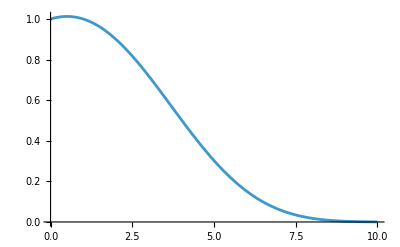

```mathematica
k=10;
Plot[(Binomial[k,d]Factorial[d])/k^d,{d,0,k},PlotRange->All]
```

#### Conjecture Code

```mathematica
ClearAll[computeTable,plotTable,gridTable]
```

```mathematica
computeTable[λ_,d_,μ_]:=
Module[
{πs,βs,tensors},

If[Not[containsIsotypicComponentQ[ConstantArray[λ,d],μ]],Return[{{},{},{}}]];

πs=IntegerPartitions[d,2λ+1];
βs=validPaths[ConstantArray[λ,d],μ];

tensors=Outer[ClebschGordanTensor[ConstantArray[λ,d],#2,#1]&,πs,βs,1];

tensors=Map[Boole[Not[Total[Abs[#],∞]==0]]&,tensors,{2}];

{πs,βs,tensors}
]
```

```mathematica
plotTable[{πs_,βs_,table_},labelsQ_]:=
Module[
{rowTicks,colnTicks},

rowTicks=Transpose[{Range[Length[πs]],πs}];
colnTicks=Transpose[{Range[Length[βs]],MatrixForm/@βs}];

ArrayPlot[table,FrameTicks->If[labelsQ,{rowTicks,Range[Length[βs]],Range[Length[πs]],colnTicks},None],Mesh->True,Frame->True,ImageSize->1->32]
]
```

```mathematica
gridTable[data_,labelsQ_]:=Grid[Map[plotTable[#,labelsQ]&,data,{2}]]
```

#### Conjecture Examples: Fixed d=2,3,4,...

```mathematica
d=2;
fixedD2=Table[computeTable[λ,d,μ],{λ,0,6},{μ,0,λ d}];
```

```mathematica
(*Note that for d=2, the CG tensor is either completely annihilated or completely preserved via the evidence below. We should prove this via the symmetry properties of the CG tensor (this should be easy) and then build this into our algorithm. Recall that for our algorithm the part sizes will really only be like 1,2,3, small integers... but we should write the code in general just in case.*)
```

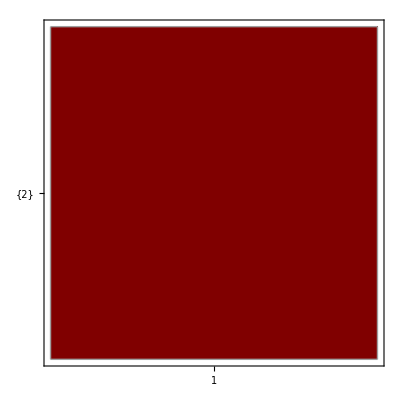
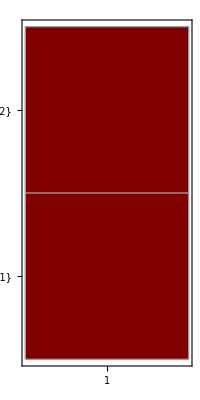
-Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gridTable[fixedD2,True]
```

```mathematica
d=3;
fixedD3=Table[computeTable[λ,d,μ],{λ,0,5},{μ,0,λ d}];
```

```mathematica
dimensionConstraint[row_]:=
With[
{λ=row[[1,2,1,1]],d=row[[1,1,1,1]],upperBounds=Transpose@(Total[#[[3]],{2}]&/@row)},
{vars=Table[Subscript[a, i],{i,0,λ d}],lowerBounds=Unitize[upperBounds]},
Solve[vars.(2Range[0,λ d]+1)==SchurS[#[[1]],ConstantArray[1,2λ+1]]∧And@@Thread[#[[2]]<=vars<=#[[3]]],vars,Integers]&/@Transpose[{row[[1,1]],lowerBounds,upperBounds}]
]
```

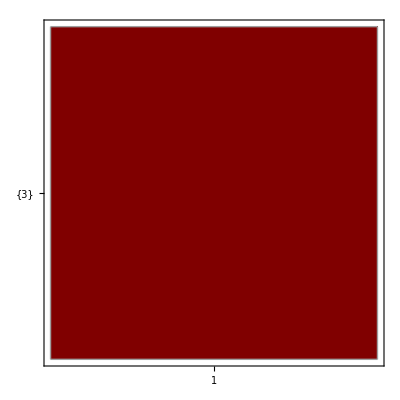
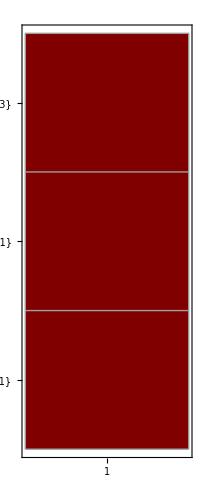
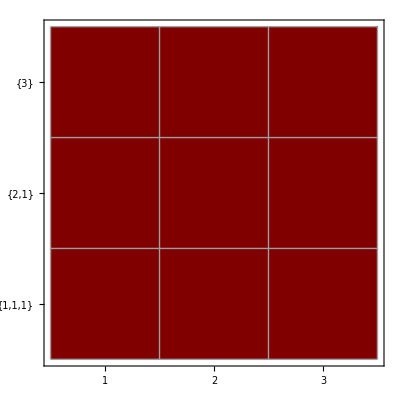
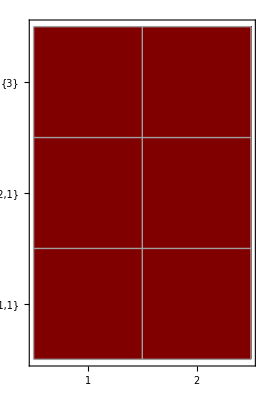
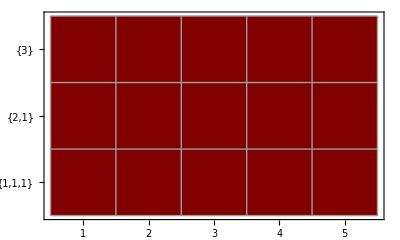
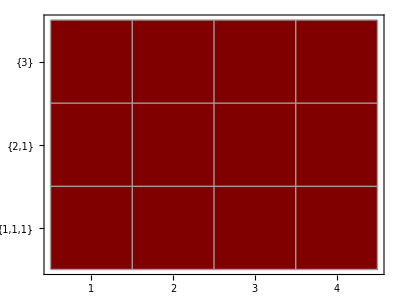
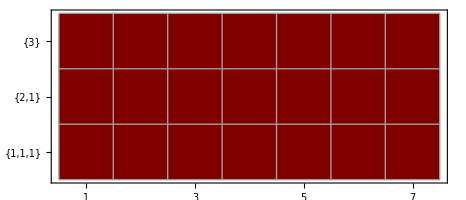
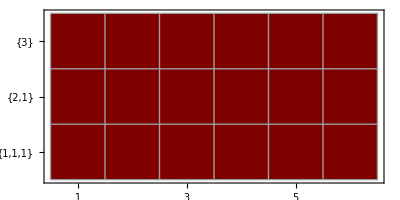
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gridTable[fixedD3,True]
```

```mathematica
d=4;
fixedD4=Table[computeTable[λ,d,μ],{λ,0,4},{μ,0,λ d}];
```

```mathematica
dimensionConstraint[fixedD4[[2]]]
```

$Aborted

```mathematica
gridTable[fixedD4,True]
```

-Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Conjecture Examples: Fixed μ=λ d,λ d-1,...,λ d-δ,...

```mathematica
δ=0;
fixedδ0=Table[computeTable[λ,d,λ d-δ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ0,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
δ=1;
fixedδ1=Table[computeTable[λ,d,λ d-δ],{λ,1,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ1,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
δ=2;
fixedδ2=Table[computeTable[λ,d,λ d-δ],{λ,1,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ2,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
δ=3;
fixedδ3=Table[computeTable[λ,d,λ d-δ],{λ,2,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ3,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
δ=4;
fixedδ4=Table[computeTable[λ,d,λ d-δ],{λ,2,6},{d,2,4}];
```

```mathematica
gridTable[fixedδ4,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Conjecture Examples: Fixed μ=0,1,2,...

```mathematica
μ=0;
fixedμ0=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ0,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
μ=1;
fixedμ1=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ1,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
μ=2;
fixedμ2=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ2,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
μ=3;
fixedμ3=Table[computeTable[λ,d,μ],{λ,0,6},{d,2,4}];
```

```mathematica
gridTable[fixedμ3,True]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Conclusions

λ | d | μ | Observations | Proof
* | * | * | # μ=λ d | Easy
* | 2 | * | Alternates between symmetric and antisymmetric | Should be easy
* | 3 | * | First columns add (2,2,0) | □
* | 4 | * | □ | □
* | * | λ d | These work by adding (1,2,3,...,d)!!!! | □
* | * | λ d-1 | □ | □
* | * | λ d-2 | □ | □
* | * | λ d-3 | □ | □

Conjecture: For all d, there exists sufficiently large λ_d such that for all λ>=λ_d, the pattern is regular.

#### Pruning

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
rowInsertionTableau[word_]:=TransposeTableau[Fold[InsertIntoTableau[#2,#1]&,{},Reverse[word]]]
columnInsertionTableau[word_]:=Fold[InsertIntoTableau[#2,#1]&,{},word]
```

```mathematica
word[λ_Integer?NonNegative,γs_List?VectorQ]:=Differences[Prepend[γs,0]]
```

```mathematica
JMEigenvalues[λ_Integer?NonNegative,γs_List?VectorQ]:=(Differences[#(#+1)&@Prepend[γs,0]]-λ(λ+1))/2
```

```mathematica
AncestralNestTree[{MapThread[Length/@columnInsertionTableau[Reverse@word[##]]&,{ΛX,#[[6]]}]}&,tree];
```

Part::partw: Part 6 of {tree} does not exist.

MapThread::mptd: Object ΛX at position {2, 1} in MapThread[Length/@columnInsertionTableau[Reverse[word[##1]]]&,{ΛX,{tree}⟦6⟧}] has only 0 of required 1 dimensions.

#### Example Code

```mathematica
ClearAll[example]
```

```mathematica
example[ΛX_,ΜX_,ν_,D_,f_]:=
Module[
{tree,numModes,dim=3,labels={i,j,k,l,m,n},a},

tree=First[TreeData/@TreeLeaves[generateTree[ΛX,ΜX,ν,D]]];
numModes=Total[ΛX ΜX];
labels=Take[labels,numModes];
a=Symmetrize[Table[Subscript[x,Sequence@@labels],Evaluate[Sequence@@({#,1,dim}&/@labels)]],Symmetric[Range[numModes]]];
FullSimplify[
f[a]/TensorContract[TensorProduct[Sequence@@ConstantArray[a,D],tree],Transpose[Partition[Range[2*numModes*D],numModes*D]]],
If[numModes==2,Tr[a]==0]
]
]
```

#### Example (Degree 2 scalar invariant of a vector)

```mathematica
example[{1},{1},0,2,Total[#^2]&]
```

{-1.73205}

#### Example (Degree 2 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,2,Tr[#.#]&]
```

{2.23607}

#### Example (Degree 3 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,3,Det[#]&]
```

{-0.569275}

#### Semistandard Young Tableaux Enumerator https://github.com/PerAlexandersson/Mathematica-packages/blob/master/NewTableaux.m

```mathematica
isEdgeQ[p_List,q_List]:=Min[p-q]>=0&&Min[q[[;;-2]]-p[[2;;]]]>=0;
```

```mathematica
pathToSSYT[pathIn_List]:=
Module[
{path,nrows,m},

{m,nrows}=Dimensions[pathIn];

path=Prepend[pathIn,ConstantArray[0,nrows]];

Table[Join@@Table[ConstantArray[If[e-1==0,None,e-1],path[[e+1,r]]-path[[e,r]]],{e,m}],{r,nrows}]
];
```

```mathematica
SemiStandardYoungTableaux[lam_List,max_Integer]:=Join@@Table[SemiStandardYoungTableaux[lam,w],{w,IntegerPartitions[Tr[lam],max]}]
```

```mathematica
SemiStandardYoungTableaux[lam_List,w_List]/;(Tr[lam]!=Tr[w]∨lam=={}):={};
```

```mathematica
SemiStandardYoungTableaux[lam_List,w_List]:=
Module[
{partitionLevels,directedEdges,mid,mu,ssytPaths,g},

mu=ConstantArray[0,Length[lam]];

mid=Table[IntegerPartitions[wi,{Length[lam]},Range[0,Max[lam]]],{wi,Most[Accumulate[w]]}];

partitionLevels=Join[{{mu}},mid,{{lam}}];

directedEdges=Join@@Table[
Join@@Outer[
If[isEdgeQ[#2,#1],DirectedEdge[{#1,lvl-1},{#2,lvl}],Nothing]&,partitionLevels[[lvl-1]],partitionLevels[[lvl]],1
],
{lvl,2,Length[partitionLevels]}
];

g=Graph[directedEdges];

ssytPaths=If[
Or[!MemberQ[VertexList[g],{mu,1}],!MemberQ[VertexList[g],{lam,Length[w]+1}]],
{},
FindPath[g,{mu,1},{lam,Length[w]+1},Infinity,All]
	];

Map[pathToSSYT[First/@#]&,ssytPaths]
];
```

```mathematica
{{□}, {□}}
```

## Young Symmetrizer

Definition (Young Symmetrizer, SSYT Basis): Let π be an integer partition of d, and let T_π be the associated Young tableau filled in increasing order. The row group and column group are defined to be

R_π:={σ∈𝔖^d|σ preserves every row of T_π}=⟨{ρ_j}_j⟩,
C_π:={σ∈𝔖^d|σ preserves every column of T_π}=⟨{γ_k}_k⟩,

where the ρ_j (resp. γ_k) are a complete set of adjacent transpositions in each row (resp. column). The row, column, and Young symmetrizers are the elements

r_π:=1/(|R_π|)∑_(σ∈R_π) σ,
c_π:=1/(|C_π|)∑_(σ∈C_π) sgn(σ)σ,
e_π:=(|R_π||C_π|)/HL_π r_π c_π,

in ℝ[𝔖^d], where HL_π is the hook length of π.

Moreover, let H be a vector space with basis {e_1,...,e_n}. Then

{e_π(⊗_(j=1)^d T_j)|T SSYT of shape π with entries from {e_1,...,e_n}}

is a basis for e_π(H^(⊗d)).

## Clebsch-Gordan

#### Theory

ClebschGordanTensor[(λ_j)_(j=1)^d,(γ_j)_(j=1)^d]:=∏_(j=1)^(d-1) (γ_j | λ_(j+1) | γ_(j+1)
s_j | m_(j+1) | s_(j+1))
s_j=m_1+...+m_j
|γ_(j+1)-γ_j|<=λ_(j+1)<=γ_(j+1)+γ_j,1<=j<=d-1
-λ_j<=m_j<=λ_j,1<=j<=d
-γ_j<=s_j<=γ_j,1<=j<=d

Theorem (Clebsch-Gordan Decomposition): The isotypic decomposition of H_λ_1⊗H_λ_2 is

H_λ_1⊗H_λ_2≅⊕_(γ_2=|λ_1-λ_2|)^(λ_1+λ_2)H_γ_2.

Definition (Iterated Multiplicity Table): Let ℐ be the Listable function defined as follows. For any λ_1,λ_2∈Λ,

ℐ(λ_1,λ_2):=Range[|λ_1-λ_2|,λ_1+λ_2].

For any λ_1,...,λ_(d-1),λ_d∈Λ,

ℐ(λ_1,...,λ_(d-1),λ_d):=ℐ(ℐ(λ_1,...,λ_(d-1)),λ_d).

Definition (Valid Paths): Let λ_1,...,λ_d∈Λ. For any index α into ℐ(λ_1,...,λ_d), define

γ_1(α):=λ_1,
γ_j(α):=|γ_(j-1)(α)-λ_j|+α_(j-1)-1,

where 2<=j<=d. We say that a given γ=(γ_1,...,γ_d)∈Λ^d is a valid path to γ_d if there exists an index α into ℐ(λ_1,...,λ_d) such that γ_j=γ_j(α) for all 1<=j<=d. Given any ν∈Λ, we define

VP_ν:=Span{γ∈Λ^d|γ valid path to ν}

to be the space of formal linear combinations of valid paths to ν.

Theorem (Iterated Clebsch-Gordan Decomposition): The isotypic decomposition of H_λ_1⊗...⊗H_λ_d is

H_λ_1⊗...⊗H_λ_d≅⊕_(ν∈Λ)H_ν⊗VP_ν.

Lemma: Let s_d:=∑_(j=1)^d λ_j and m_d:=max_(j=1)^d λ_j. Let L_d:=max{0,2 m_d-s_d}. The ν that show up are Λ_((λ_j)_j):={L_d,...,s_d}.

#### Computation

Proposition (Angular Momentum Basis): Let

1,1:=1/(√2)(-1
-ⅈ
0),J_-:=1/(√2)(0 | 0 | 1
0 | 0 | -ⅈ
-1 | ⅈ | 0).

For any nonzero λ∈Λ, let

𝒥_-:=∑_(l=0)^(λ-1) 𝟙^(⊗l)⊗J_-⊗𝟙^(⊗λ-1-l).

For any integer -λ<=m<λ, let

λ,m:=√(((λ+m)!)/((2λ)!(λ-m)!))𝒥_-^(λ-m)(1,1)^(⊗λ).

Then {λ,m}_(-λ<=m<=λ) is an orthonormal basis for H_λ.

Definition (Clebsch-Gordan Tensor): The Clebsch-Gordan tensor

CG_γ_2^(λ_1,λ_2)∈H_λ_1^*⊗H_λ_2^*⊗H_γ_2

is the unique linear surjection whose coordinate at λ_1,m_1,λ_2,m_2,γ_2,m is the Clebsch-Gordan coefficient ClebschGordan[{λ_1,m_1},{λ_2,m_2},{γ_2,m}].

Definition (Iterated Clebsch-Gordan Tensor): Let γ be a valid path to ν. Arrange the Clebsch-Gordan tensors

CG_γ_j^(γ_(j-1),λ_j)∈H_(γ_(j-1))^*⊗H_λ_j^*⊗H_γ_j

into a straight-path tensor network, contract, and tensor with γ∈VP_ν to obtain the iterated Clebsch-Gordan tensor

CG_γ^λ∈H_λ_1^*⊗...⊗H_λ_d^*⊗H_ν⊗VP_ν.

Proposition (Angular Momentum Basis to Monomial Basis): The iterated Clebsch-Gordan tensor converts the angular momentum basis on H_λ to the angular momentum basis on H_1^(⊗λ). Let U:H_1->H_1 convert the angular momentum basis on H_1 to the monomial basis on H_1. Then U^(⊗λ) converts the angular momentum basis on H_1^(⊗λ) to the monomial basis on H_1^(⊗λ). These should still be symmetric and trace free, hence they should form a monomial basis for H_λ⊆H_1^(⊗λ).

## Proofs

#### Question for Prof. Ben-Zvi

Let H_λ be the SO(3)-irrep of dimension 2λ+1. Let d∈ℕ, let π be a partition of d, and let e_π be a Young symmetrizer with shape π. We know that iterated Clebsch-Gordan yields the isotypic decomposition

H_λ^(⊗d)≅⊕_μ H_μ⊗Hom_(SO(3))(H_μ,H_λ^(⊗d)).

Moreover, an explicit basis for the multiplicity space Hom_(SO(3))(H_μ,H_λ^(⊗d)) is indexed by the collection of valid paths γ:=(γ_j)_(j=1)^d starting at γ_1=λ and ending at γ_d=μ, where each valid path γ corresponds to the tensor

CG(γ):=∏_(j=1)^(d-1) (γ_j | λ | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈Hom_(SO(3))(H_μ,H_λ^(⊗d)),
s_j:=m_1+...+m_j.

Define

f(π,γ):=Piecewise[{{1, e_π(CG(γ))!=0}, {0, e_π(CG(γ))=0}}].

We wish to obtain a fast combinatorial/algorithmic way to evaluate f (faster than directly computing e_π(CG(γ)), which is expensive). In other words, we wish to understand which parts of the multiplicity space Hom_(SO(3))(H_μ,H_λ^(⊗d)) “survive” after applying the Young symmetrizer e_π, which leaves behind

e_π(H_λ^(⊗d))≅∑_μ H_μ⊗Hom_(SO(3))(H_μ,e_π(H_λ^(⊗d))).

Many examples are below. In each diagram, the rows are indexed by partitions π, the columns are indexed by valid paths γ, a black square indicates that f(π,γ)=1, and a white square indicates that f(π,γ)=0.

CG(γ) IS INJECTIVE!!! But e_π CG(γ) must be zero or injective. That is, Im CG(γ) and ker e_π cannot intersect. Lets normalize our Young symmetrizer so that it is actually idempotent and check.

Proof: First, it is clear that 𝒥_- preserves symmetry. Moreover, since J_- is antisymmetric, 𝒥_- preserves the property of being trace free. Now, note that λ,λ=(f_+)^(⊗λ)∈H_λ is normalized.

J_-f_+=f_0,
J_-f_0=f_-,
J_-f_-=0.

Proof (Isotypic Decomposition): Define the isotypic component

X_λ:=∑_(f∈Hom(H_λ,X)) f(H_λ)

We claim that the evaluation map

E:H_λ⊗M_λ->X_λ
v⊗f↦f(v)

is an isomorphism of representations. By the universal property of the tensor product, E is a well defined linear map. Clearly, E is surjective. By a dimension count, E is injective. Since the maps in M_λ are equivariant, E is equivariant. Now, since X is completely reducible and {H_λ}_(λ∈Λ) is complete,

X=∑_(λ∈Λ) X_λ.

Fix π,λ∈Λ such that X_λ∩X_π!=0. Since X_λ∩X_π is finite dimensional, it is completely reducible, so it contains a nonzero irreducible representation W. Show that W≅H_λ and W≅H_π. Since {H_λ}_(λ∈Λ) is independent, λ=π. Thus, the sum is direct.

Proof (Maps Between Isotypic Components):

Hom(H_λ⊗M_λ,H_π⊗N_π)≅((H_λ⊗M_λ)^*⊗(H_π⊗N_π))^G
≅((V_λ^*⊗H_π)⊗(M_λ^*⊗N_π))^G
≅(V_λ^*⊗H_π)^G⊗(M_λ^*⊗N_π)
≅Hom(H_λ,H_π)⊗Hom(M_λ,N_π)
≅Piecewise[{{0, λ!=π}, {Hom(M_λ,N_π), λ=π}}]

Proof (Nakayama’s Lemma): (⟹) Let i be the smallest nonnegative integer such that M^D!=0. Note that every element in I M has degree at least i+1, so M^D⊈I M. Thus, if M=I M, then M=0. Now, let N be the submodule generated by m_1,...,m_n∈M. See Wikipedia.

(⟸) Fix m+I M∈M/I M. Write m=∑_i r_i m_i for r_i∈R. Write r_i=a_i+b_i for a_i∈ℝ and b_i∈I. Then m+I M=∑_i a_i(m_i+I M).

## Temp Storage

#### Problem For ChatGPT

Recall that

e_π_λ(H_λ^(⊗d_λ))≅⊕_(μ_λ∈Λ_Table[λ,d_λ])H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))).

Recall that it is easy to obtain a valid path basis {β} for VP_μ_λ^(λ,d_λ) by enumerating all valid Clebsch-Gordan paths from λ to μ_λ. Provide a combinatorial algorithm to determine whether a given basis vector β∈VP_μ_λ^(λ,d_λ) and a given Young projector e_(π_λ,μ_λ) satisfy e_(π_λ,μ_λ)(β)=0. In other words, provide a combinatorial algorithm to determine whether β∈e_(π_λ,μ_λ)(VP_μ_λ^(λ,d_λ)). The algorithm should not rely on computing many 3j or 6j coefficients; in particular, it is unsatisfactory to explicitly compute Clebsch-Gordan tensors via 3j coefficients and directly apply the Young symmetrizer, and it is unsatisfactory to apply the Young symmetrizer directly on VP_μ_λ^(λ,d_λ) by passing the symmetric group action to VP_μ_λ^(λ,d_λ) via 6j coefficients. I would like a combinatorial algorithm in terms of β and π_λ only. It is known that a single β can be smeared out over multiple isotypic components, i.e., over multiple π_λs.

#### Scratch

We know that

⊕_ν H_ν⊗VP_ν^(d+1)≅H_λ^(⊗d+1)≅⊕_μ H_μ⊗H_λ⊗VP_μ^(λ,d)≅⊕_ν H_ν⊗⊕_(|μ-ν|<=λ)VP_μ^(λ,d),

so

⊕_(|μ-ν|<=λ)VP_μ^d≅VP_ν^(d+1)

via

(λ,...,μ)↦(λ,...,μ,ν).

We know that

⊕_μ H_μ⊗VP_μ^d≅H_λ^(⊗d)≅⊕_(π⊢d)e_π(H_λ^(⊗d))⊗[π]≅⊕_(π⊢d)⊕_μ H_μ⊗e_(π,μ)(VP_μ^d)⊗[π]≅⊕_μ H_μ⊗(⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]),

so

VP_μ^d≅⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π].

Thus,

⊕_(|μ-ν|<=λ)⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]≅⊕_(π'⊢d+1)e_(π',ν)(VP_ν^(d+1))⊗[π'].

```mathematica
(*ms=
AncestralNestTree[
With[{s=Total[#],j=Length[#]},Range[Max[-λs[[j]],-γs[[j]]-s],Min[λs[[j]],γs[[j]]-s]]]&,
Tree[0,None],
Length[λs]
];

ms=Rest/@TreeData/@TreeLeaves[AncestralNestTree[{#}&,ms]];*)
```

```mathematica
(*Put these two functions together at the end!!*)
```

```mathematica
ClearAll[CGTensor]
CGTensor[γ1_Integer?NonNegative,λ2_Integer?NonNegative,γ2_Integer?NonNegative]:=
CGTensor[γ1,λ2,γ2]=
SymmetrizedArray[
Join@@Table[
{1+γ1+m1,1+λ2+m2,1+γ2+m1+m2}->ClebschGordan[{γ1,m1},{λ2,m2},{γ2,m1+m2}],
{m1,-γ1,γ1},{m2,Max[-λ2,-γ2-m1],Min[λ2,γ2-m1]}
],
{2γ1+1,2λ2+1,2γ2+1}
]
CGTensor[λs_List?VectorQ,γs_List?VectorQ]/;
First[λs]==First[γs]∧
Length[λs]>=1∧
Length[λs]==Length[γs]∧
Abs[ListConvolve[{1,-1},γs]]\[VectorLessEqual]Rest[λs]\[VectorLessEqual]ListConvolve[{1,1},γs]:=
If[
Length[λs]==1,
IdentityMatrix[2First[λs]+1,SymmetrizedArray],
Dot@@MapThread[CGTensor,{Most[γs],Rest[λs],Rest[γs]}]
]
```

Proposition: Define

A_R:=(ρ_j-𝟙)_j,
A_C:=(γ_k+𝟙)_k,
Fix(R_π):={v∈⊗_(j=1)^d V_j|∀σ∈R_π,σ v=v}={v∈⊗_(j=1)^d V_j|∀j,ρ_j v=v}=ker A_R
Alt(C_π):={v∈⊗_(j=1)^d V_j|∀σ∈C_π,σ v=sgn(σ)v}={v∈⊗_(j=1)^d V_j|∀k,γ_k v=-v}=ker A_C

Then r_π,c_π∈ℝ[𝔖^d] are orthogonal projections onto Fix(R_π),Alt(C_π). Moreover, e_π is a projection. To apply e_π, we need to project first onto ker A_C then onto ker A_R.

Enumerate the set {(d_λ)_(λ∈Λ_X)|d_λ∈ℕ_0,∑_(λ∈Λ_X) d_λ=D} of weak compositions of D with |Λ_X| parts using D stars and |Λ_X|-1 bars.

For each (d_λ)_λ, enumerate the set {(π_λ)_(λ∈Λ_X)|π_λ⊢d_λ,l(π_λ)<=min(dim H_λ,dim M_λ)} of tuples of partitions.

For each (d_λ)_λ, enumerate the set {(μ_λ)_(λ∈Λ_X)|μ_λ∈Λ_(λ,d_λ)} of tuples of labels.

```mathematica
Graph[{"D"->"(d_λ)_λ","(d_λ)_λ"->"(π_λ)_λ","(d_λ)_λ"->"(μ_λ)_λ","(d_λ)_λ"->"(β_λ)_λ","(d_λ)_λ"->"(α_λ)_λ","ν"->"(μ_λ)_λ","ν"->"γ","(μ_λ)_λ"->"γ","(μ_λ)_λ"->"(β_λ)_λ","(π_λ)_λ"->"(α_λ)_λ","γ"->"CG_ν^((SubscriptBox[μ, λ])_λ)","(β_λ)_λ"->"CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)","(π_λ)_λ"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_ν^((SubscriptBox[μ, λ])_λ)"->"CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])","CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])"->"End","(α_λ)_λ"->"End"},VertexLabels->Placed["Name",Center],VertexSize->0.8]
```

Graph[{D->(d_λ)_λ,(d_λ)_λ->(π_λ)_λ,(d_λ)_λ->(μ_λ)_λ,(d_λ)_λ->(β_λ)_λ,(d_λ)_λ->(α_λ)_λ,ν->(μ_λ)_λ,ν->γ,(μ_λ)_λ->γ,(μ_λ)_λ->(β_λ)_λ,(π_λ)_λ->(α_λ)_λ,γ->CG_ν^((SubscriptBox[μ, λ])_λ),(β_λ)_λ->CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ),(π_λ)_λ->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_((SubscriptBox[μ, λ])_λ)^((λ, SubscriptBox[d, λ])_λ)->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_ν^((SubscriptBox[μ, λ])_λ)->CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ]),CG_ν^(π SubscriptBox[(λ, SubscriptBox[d, λ]), λ])->End,(α_λ)_λ->End},VertexLabels→Placed[Name,Center],VertexSize→0.8]

Thus, since e_π is G-equivariant, we have

e_π(H_λ^(⊗d_λ))≅⊕_(μ∈Λ_(d,λ))H_μ⊗e_(π,μ)(VP_μ^(λ,d_λ))

for some linear maps e_(π,μ) on VP_μ^(λ,d_λ). Note that H_μ⊗e_(π,μ)(VP_μ^(λ,d_λ)) embeds into e_π(H_λ^(⊗d_λ)) by a Clebsch-Gordan isometry.

Theorem (Isotypic Decomposition of the Symmetric Power): Suppose that X has the isotypic decomposition

X≅⊕_λ H_λ⊗M_λ.

Then 𝒮^D(X) has the isotypic decomposition

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗N_ν^D,

where

N_ν^D:=⊕_(∑_λ d_λ=D)⊕_((μ_λ∈Λ_(d,λ))_λ)Hom_G(H_ν,⊗_λ H_μ_λ)⊗⊗_λ(⊕_(π⊢d_λ)VP_μ_λ^(λ,d_λ)⊗e_π(M_λ^(⊗d_λ))).

Lemma (Basis for VP_ν^((μ_λ)_λ)): For any (μ_λ∈Λ_(d,λ))_(λ∈Λ_X) and ν∈Λ_X, the vector space VP_ν^((μ_λ)_λ) has basis given by all paths in indexPaths.

J_1:=(  |   |  
  |   | -ⅈ
  | ⅈ |  ),J_2:=(  |   | ⅈ
  |   |  
-ⅈ |   |  ),J_3:=(  | -ⅈ |  
ⅈ |   |  
  |   |  ),J_±:=1/(√2)(J_1±ⅈ J_2)=1/(√2)(  |   | ∓1
  |   | -ⅈ
±1 | ⅈ |  ).

Proposition: Depth[ℐ(a_1,...,a_d)]=Depth[a_1]+...+Depth[a_d].

Theorem (Isotypic Decomposition): X has the isotypic decomposition

X≅⊕_λ H_λ⊗M_λ,

where Λ_X:={λ∈Λ|M_λ!=0}⊆Λ is finite and

M_λ:=(H_λ^*⊗X)^G≅Hom^G(H_λ,X).

Definition: Let

A:=⊕_(Y irrep of G)(𝒮(X^*)⊗Y)^G

be the covariant algebra of X.

Remark: For certain specific X, Sahil has obtained (non-minimal) generating sets for A as an ℝ-algebra. These generating sets can be cut down to generating sets for M as an R-module, but the process is computationally expensive.

Definition:  The tensor algebra on V is the graded ℝ-algebra

𝒯(V):=⊕_(d∈ℕ_0)𝒯^d(V),
𝒯^d(V):=V^(⊗d).

The symmetrization map on 𝒯(V) is the linear map

Sym:𝒯(V)->𝒯(V),
v_1⊗…⊗v_d↦1/(d!)∑_(σ∈Σ_d) v_(σ(1))⊗…⊗v_(σ(d)).

The symmetric algebra on V is the commutative graded ℝ-algebra

𝒮(V):=Sym(𝒯(V))=⊕_(d∈ℕ_0)𝒮^d(V),
𝒮^d(V):=Sym(𝒯^d(V)),

with multiplication given by the shuffle product

⊙:𝒮(V)×𝒮(V)->𝒮(V),
(a,b)↦a⊙b:=Sym(a⊗b).

Lemma: Let G act linearly on vector spaces V,{V_α}_α. Then

g∈G acts on φ∈V^* by g φ:=φ∘g^-1,

g∈G acts on ⊕_α v_α∈⊕_α V_α by g⊕_α v_α:=⊕_α g v_α, and

g∈G acts on ⊗_α v_α∈⊗_α V_α by g⊗_α v_α:=⊗_α g v_α provided that the tensor product over α is finite.

Moreover, with respect to the above actions, there exist equivariant isomorphisms (which necessarily have equivariant inverses)

(⊕_α V_α)⊗V≅⊕_α(V_α⊗V) and

(⊕_α V_α)^*≅⊕_α V_α^* provided that the sum over α is finite.

Lemma: Let V,M be representations of G.

If M is fixed by G, then (V⊗M)^G=V^G⊗M.

Hom(V,M)≅(V^*⊗M)^G.

Lemma (Schur): Let V,W be irreducible representations of G, and let φ∈Hom(V,W). Then φ=0 or φ is an isomorphism. In particular, either Hom(V,W)=0 or Hom(V,W)≅ℂ.

Remark: To motivate the definition of 𝒮(X^*)⊗Y, consider the pairing (𝒮(X^*)⊗Y)×X->Y defined on elementary tensors (which correspond to the component functions of the polynomial) by

(φ⊗y,x)↦(φ⊗y)(x):=φ(x)y

and extended linearly to 𝒮(X^*)⊗Y, where φ(x) is defined by writing

φ=⊕_(d=0)^D⊕_(j_1,...,j_d=1)^(dim X^*)φ_(j_1... j_d)e_j_1^*⊗…⊗e_j_d^*

in terms of a basis {e_j^*}_(j=1)^(dim X^*) for X^* and declaring that

φ(x):=⊕_(d=0)^D⊕_(j_1,...,j_d=1)^(dim X^*)φ_(j_1... j_d)e_j_1^*(x)*…*e_j_d^*(x).

Note that φ(x) is a degree D polynomial in the entries of X selected by the e_j^*.

To motivate the definition of (𝒮(X^*)⊗Y)^G, fix g∈G, ∑_i φ_i⊗y_i∈𝒮(X^*)⊗Y, and x∈X. Observe that

(∑_i φ_i⊗y_i)(g x)=g((∑_i φ_i⊗y_i)(x))
⟺∑_i φ_i(g x)y_i=g(∑_i φ_i(x)y_i)
⟺∑_i (g^-1 φ_i)(x)y_i=∑_i φ_i(x)g y_i
⟺(∑_i g^-1 φ_i⊗y_i)(x)=(∑_i φ_i⊗g y_i)(x).

Thus, we conclude that ∑_i φ_i⊗y_i is equivariant iff g∑_i φ_i⊗y_i=∑_i φ_i⊗y_i for all g∈G iff ∑_i φ_i⊗y_i∈(𝒮(X^*)⊗Y)^G.

Proposition: R is a graded subalgebra of 𝒮(X^*). If conditions, then M is a finitely generated graded R-module.

Proof: First, note that

R:=(𝒮(X^*))^G=⊕_(d∈ℕ_0)(𝒮^d(X^*))^G.

Thus, R is a graded subspace of S(X^*). Moreover, since the tensor product and the symmetrization map are equivariant, the shuffle product is equivariant, so R is closed under multiplication, and moreover the multiplication respects the grading.

Next, define the scalar multiplication

R×M->M
(r,φ⊗y)↦(r⊙φ)⊗y

on elementary tensors in M, and extend the multiplication linearly to all of M. Since the shuffle product is equivariant, the scalar multiplication is well defined. That M is a graded R-module follows easily. That M is finitely generated follows from conditions.

Theorem (Maps Between Isotypic Components): Let X,Y be representations with isotypic decompositions

X≅⊕_(λ∈Λ)H_λ⊗M_λ,
Y≅⊕_(λ∈Λ)H_λ⊗N_λ.

Then for any π,λ∈Λ,

Hom(H_λ⊗M_λ,H_π⊗N_λ)≅δ_(λ π)Hom(M_λ,N_π).

Moreover, the R-module multiplication

R⊗M->M

corresponds to the multiplication

N_(0,d)⊗N_(ρ,e)->N_(ρ,d+e),
n_(0,d)⊗n_(ρ,e)↦SOMETHING

on each graded piece in the isotypic decomposition.

Definition: Given λ_1,...,λ_d∈Λ, define T_(λ_1,...,λ_d) be the corresponding left associate binary tree defined recursively as follows:

there are d leaf nodes containing the data λ_1,...,λ_d from left to right, and

each parent node with left child a_1 and right child a_2 contains the data ℐ(a_1,a_2).

Given ℛ_D,ℳ_D for all D=0,1,2,...

For D=1,2,...

For D'=1,2,...,D

For r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D'), multiply r_D' with m_(D-D') as monomials

#### Reduce to finding a basis for the subspace of monomials

Theorem 1 (https://arxiv.org/abs/2406.01552): Write X as the direct sum

X=⊕_(j=1)^J X_j

of irreducible representations X_j. There exists an equivariant isomorphism of graded ℝ-algebras

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

which restricts to an equivariant isomorphism of graded ℝ-algebras

R=(𝒮(X^*))^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*)^G.

There exists an equivariant isomorphism of graded ℝ-modules and graded R-modules

𝒮(X^*)⊗Y≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*⊗Y,

which restricts to an equivariant isomorphism of graded ℝ-modules and graded R-modules

M=(𝒮(X^*)⊗Y)^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*⊗Y)^G.

Proof: First, observe that

𝒯(X^*)=⊕_(d∈ℕ_0)𝒯^d(X^*)=⊕_(d∈ℕ_0)(X^*)^(⊗d)≅⊕_(d∈ℕ_0)(⊕_(j=1)^J X_j^*)^(⊗d)≅⊕_(d∈ℕ_0)⊕_(j_1,...,j_d=1)^J X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is still the ordinary tensor product. Symmetrizing yields Eq. (1),

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=...<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is defined by declaring the product of X_j_1^*⊗…⊗X_j_d^* and X_k_1^*⊗…⊗X_k_e^* to be X_j_1^*⊗…⊗X_j_d^*⊗X_k_1^*⊗…⊗X_k_e^* with the indices reordered to be nondecreasing.

Corollary: The monomial parts of an equivariant polynomial are equivariant.

𝒮^d_λ(H_λ⊗M_λ)=((H_λ⊗M_λ)^(⊗d_λ))^(𝔖^d_λ)≅(H_λ^(⊗d_λ)⊗M_λ^(⊗d_λ))^(𝔖^d_λ)
≅^(Schur-Weyl duality)((⊕_(π∈P(d_λ,h_λ))e_π(H_λ^(⊗d_λ))⊗[π])⊗(⊕_(π∈P(d_λ,m_λ))e_π(M_λ^(⊗d_λ))⊗[π]))^(𝔖^d_λ)
≅^(Schur Lemma)⊕_(π⊢d_λ)e_π(H_λ^(⊗d_λ))⊗e_π(M_λ^(⊗d_λ)),

#### Isotypic decomposition of the tensor product, d=2 (Clebsch–Gordan Theory)

Definition (Clebsch-Gordan Intertwiner): Let δ∈𝒮^2(V) be the Kronecker delta, and let ϵ∈𝒯^3(V) be the Levi-Civita tensor. For a,b>=1, define contraction with δ as

Tr_δ:𝒮^(a+b)(V^*)->𝒮^(a+b-2)(V^*),
f↦f(δ),

and contraction with ϵ as

Tr_ϵ:𝒮^a(V^*)⊗𝒮^b(V^*)->𝒮^(a+b-1)(V^*),
f⊗g↦Sym(ϵ_i^(j k)f_(j *)g_(k *)).

Let π_ℋ:𝒮(V^*)->ℋ(V^*) be the canonical projection. Define the maps

P_δ^k:ℋ^a(V^*)⊗ℋ^b(V^*)(->)^Sym 𝒮^(a+b)(V^*)(->)^(Tr_δ^k)𝒮^(a+b-2k)(V^*)(->)^π_ℋ ℋ^(a+b-2k)(V^*),0<=k<=min{a,b},
P_(ϵ,δ)^k:ℋ^a(V^*)⊗ℋ^b(V^*)(->)^Tr_ϵ 𝒮^(a+b-1)(V^*)(->)^(Tr_δ^k)𝒮^(a+b-1-2k)(V^*)(->)^π_ℋ ℋ^(a+b-1-2k)(V^*),0<=k<=min{a,b}-1.

Proposition: Tr_δ,Tr_ϵ,π_ℋ,P_δ^k,P_(ϵ,δ)^k are surjective equivariant linear maps. Moreover, we have dual maps

Tr_δ^*:𝒮^(a+b-2)(V)->𝒮^(a+b)(V),
A↦Sym(δ⊗A),

and

Tr_ϵ^*:𝒮^(a+b-1)(V)->𝒮^a(V^*)⊗𝒮^b(V^*),
A↦(Sym⊗Sym).

Proof: Show that P_δ^k,P_(ϵ,δ)^k are surjective equivariant linear maps.

To prove Eq. (5), define

P:=⊕_(k=0)^(min{a,b})P_δ^k⊕⊕_(k=0)^(min{a,b}-1)P_(ϵ,δ)^k,

which is a surjective equivariant linear map. Thus, since

dim(ℋ^a(V^*)⊗ℋ^b(V^*))=(2a+1)(2b+1)=dim(⊕_(k=0)^(min{a,b})Im P_δ^k⊕⊕_(k=0)^(min{a,b}-1)Im P_(ϵ,δ)^k),

P is an isomorphism.

Finally, note that

(ℋ^a(V^*)⊗ℋ^b(V^*))^G≅⊕_(k=0)^(min{a,b})(ℋ^(a+b-2k)(V^*))^G⊕⊕_(k=0)^(min{a,b}-1)(ℋ^(a+b-1-2k)(V^*))^G.

If d=0, then ℝ≅ℋ^d(V^*)=(ℋ^d(V^*))^G. If d>0, then (ℋ^d(V^*))^G=0, since any nonzero v∈(ℋ^d(V^*))^G would yield a nontrivial proper sub-representation 0<Span{v}<ℋ^d(V^*), as dim ℋ^d(V^*)=2D+1>1.

Given: D,Λ_X,M_λ

Define n=|Λ_X|

Enumerate {∑_(λ∈Λ_X) d_λ=D|(‖d‖)_1=D}

Define m=|Λ_(d,λ)|=1+max_(λ∈Λ_X) λ d_λ

Enumerate {(μ_λ∈Λ_(d,λ))_(λ∈Λ_X)} using n-digit m-ary numbers in lexicographic (i.e., increasing) order (should be m^n terms)

Apply Clebsch-Gordan on ⊗_(λ∈Λ_X)H_μ_λ to determine C_0^μ and C_ρ^μ

For each λ∈Λ_X and each partition π of d_λ with

## Draft Stuff (Old)

DRAFT STUFF: Towards this, note that Sym^d is equivariant, and Tr^d is equivariant provided that G is a subgroup of O(V).

𝒯^d(V)(->)^(Sym^d)𝒮^d(V)(->)^(Tr^d)𝒮^(d-2)(V)
ℋ^d(V):=Im Sym^d∩Ker Tr^d

(𝒯^d(V))^G(->)^(Sym_G^d)(𝒮^d(V))^G(->)^(Tr_G^d)(𝒮^(d-2)(V))^G
(ℋ^d(V))^G=(Im Sym^d)^G∩(Ker Tr^d)^G=Im Sym_G^d∩Ker Tr_G^d

Suppose we have a basis ℬ for (𝒯^d(V))^G. Then Sym_G^d(ℬ) generates (𝒮^d(V))^G. Standard linear algebra can cut down provided that ℬ doesn’t have too many elements. For our use case (d=11), I expect linear systems on the order of 10^4×10^4. Not great but also not terrible.

TODO: First get basis for SO(V) and T(V). Then see if you can shortcut to automatically identify a natural basis for S(V). Count dimensions if needed. Similarly, see if you can shortcut to get a natural basis for H(V). Again count dimensions. Worst case we do the brute force solution above. Best case this method works.

#### Find a basis for (ℋ^λ(V))^(SO(3))

Definition: Let 𝒫_(O(V))(m) denote the set of perfect matchings of {1,...,m}. For any P={{i_1,j_1},...,{i_l,j_l}}∈𝒫_(O(V))(m), define σ_P∈S_(2l) to be the permutation whose two-line notation is

σ_P:=(1 | 2 | … | 2l-1 | 2l
i_1 | j_1 | … | i_l | j_l),

where the second row is ordered such that i_m<j_m for all m∈{1,...,l} and i_m<i_(m+1) for all m∈{1,...,l-1}. Further define T_P∈𝒯^m(V) to be the tensor

T_P:=σ_P((⊕_(i,j=1)^(dim V)δ_(i j)e_i⊗e_j)^(⊗l)).

Lemma 2: The set

{T_P}_(P∈𝒫_(O(V))(m))

is a basis for (𝒯^m(V))^(O(V)) of size ((2l)!)/(2^l l!).

Definition: Let 𝒫_(SO(V))(m) denote the set of non-crossing planar partitions of {1,...,m} with no singletons. For any P={B_1,...,B_j}∈𝒫_(SO(V))(m), define

T_P:=

Lemma 3: The set

{T_P}_(P∈𝒫_(SO(V))(m))

is a basis for (𝒯^m(V))^(SO(V)) of size [m^th Riordan number].

#### Find a basis for the subspace of monomials

Remark 6: Problem 3 has been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=O(V) in https://arxiv.org/abs/2406.01552. I think Problem 3 has also been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=SO(V).

Remark 7: For the turbulence application, we must solve Problem 3 for X_j=ℋ^d_j(V), Y=ℋ^d(V), and G=SO(V). That is, we have to find bases for

the space of monomial SO(3)-invariant polynomial maps from harmonic tensors to ℝ

the space of monomial SO(3)-equivariant polynomial maps from harmonic tensors to harmonic tensors

I’m not actually sure that this is so easy.

Remark 8: Appendix A in https://arxiv.org/pdf/2404.18735 shows that any invariant polynomial 𝒮^d(V)->ℝ is the restriction of an invariant polynomial 𝒯^d(V)->ℝ (however, there are polynomial extensions that are not invariant). Results like this might help.

Remark 5: We might want to investigate conditions under which the fixed set of the tensor product is the tensor product of the fixed sets (this is not true in general). This would simplify the theory and reduce the computational complexity dramatically. This would also allow for arbitrary combinations of tensors/symmetric tensors/harmonic tensors in X and Y.

For turbulence modeling, we care about the following special case.

2,2,3,4, so k=11 what

In particular, we have

ℐ(a_1,...,a_d,b_1,...,b_e)=ℐ(ℐ(a_1,...,a_d),ℐ(b_1,...,b_e)).

## Approach via Invariant Scalar Functions (Old)

The relevant module and algebra both live in a large parent module:

N | := | Invariant(⊕_j Ker(tr^n_j)⊕(V^*)^(⊗n),ℝ) | module over R
| |   | | |  
M | := | Equivariant(⊕_j Ker(tr^n_j),Sym(V^(⊗n))) | module over R
| |   | | |  
R | := | Invariant(⊕_j Ker(tr^n_j),ℝ) | algebra over ℝ

where M is embedded in N via m↦m(·)·. To obtain a minimal generating set for M, one strategy is to obtain a minimal generating set for the isomorphic copy of M in N, which consists of invariant, scalar-valued functions that are multilinear and symmetric in the components of the second argument.

$Aborted